# Degree of Polarization

## Definitions

```mathematica
P [Ioff_,Iab_,Ia_,Ib_]:= Sqrt[(Ioff-Ia)*(Ioff-Ib)/(Ioff*Iab-Ib*Ia)]
ΔP [Ioff_,Iab_,Ia_,Ib_,ΔIoff_,ΔIab_,ΔIa_,ΔIb_]:=Sqrt[(((Ib (-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)^2-(-Ib+Ioff)/(-Ia Ib+Iab Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff))))^2ΔIa^2+(((Ia (-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)^2-(-Ia+Ioff)/(-Ia Ib+Iab Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff))))^2ΔIb^2+((-(Iab (-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)^2+(-Ia+Ioff)/(-Ia Ib+Iab Ioff)+(-Ib+Ioff)/(-Ia Ib+Iab Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff))))^2 ΔIoff^2+(-(Ioff (-Ia+Ioff) (-Ib+Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)) (-Ia Ib+Iab Ioff)^2))^2ΔIab^2]
e1 [Ioff_,Iab_,Ia_,Ib_] :=(Iab-Ib)/(Ioff-Ia)
Δe1[Ioff_,Iab_,Ia_,Ib_,ΔIoff_,ΔIab_,ΔIa_,ΔIb_] := Sqrt[(((Iab-Ib)/(-Ia+Ioff)^2)*ΔIa)^2 +((-1/(-Ia+Ioff))*ΔIb)^2 +((-(Iab-Ib)/(-Ia+Ioff)^2)*ΔIoff)^2 +((1/(-Ia+Ioff))*ΔIab)^2 ]
e2 [Ioff_,Iab_,Ia_,Ib_] :=(Iab-Ia)/(Ioff-Ib)
Δe2 [Ioff_,Iab_,Ia_,Ib_,ΔIoff_,ΔIab_,ΔIa_,ΔIb_]:= Sqrt[((-1/(-Ib+Ioff))*ΔIa)^2 +(((-Ia+Iab)/(-Ib+Ioff)^2)*ΔIb)^2 +((-(-Ia+Iab)/(-Ib+Ioff)^2)*ΔIoff)^2 +((1/(-Ib+Ioff))*ΔIab)^2 ]
Flipp[CountsOff_,CountsOn_]:=CountsOff/CountsOn
ErrFlipp[CountsOff_,CountsOn_,ΔCountsOff_,ΔCountsOn_]:= Sqrt[((-CountsOff/CountsOn^2)*ΔCountsOn)^2 + ((1/CountsOn)*ΔCountsOff)^2 ]
Contrast[Imax_,Imin_]:=(Imax-Imin)/(Imax+Imin)
ErrContrast[Imax_,Imin_,ΔImax_,ΔImin_]:=Sqrt[(((2*Imin)/(Imax+Imin)^2)*ΔImax)^2+(((-2*Imax)/(Imax+Imin)^2)*ΔImin)^2]
k1[e_]:=1/2(e+1)
k2[e_]:=1/2(e+1)
Δk1[Δe_]:=1/2Δe
Δk2[Δe_]:=1/2Δe
```

## File input

Intro

```mathematica
Needs["ErrorBarPlots`"]
```

The following code will calculate all degrees of polarisation of all files in the folder matching the criteria below. All the files should have been created with the Polarimeter VI containing multiple degrees of polarisation measurements for different positions in one file.

File Import

```mathematica
(* get all files that matter in directory and import them all *)
files=FileNames["*1325-degree-of-polarisation*.dat",NotebookDirectory[]]
positions=Import[NotebookDirectory[]<>"2018-11-22-1500-degree-of-polarisation.position","Table"][[1]][[;;;;4]];
data=Import[#]&/@files;
```

{C:\Users\admin\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 22.11.2018\2018-11-23-1325-degree-of-polarisation.dat}

Calculations & Rearrangements

```mathematica
(* get the interesting intensities *)
intensities=Transpose[#[[5;;-1]]][[2]]&/@data;
intensities=Partition[#,4]&/@intensities;

(* rearrange the items to match with the required form of P [Ioff_,Iab_,Ia_,Ib_]
if measurement is sorted differently *)
Rearrange1[item_]:=item[[{1,4,2,3}]]
intensities=Map[Rearrange1,#]&/@intensities;
```

```mathematica
(* calculating the degree of polarisation for all entries *)
pol = P@@@#&/@intensities //N //Re;
(* calculate sqrt for deltas and joining the lists, then calculating deviations *)
pDelta=ΔP @@@#&/@Join[intensities,Sqrt[intensities],3] //N;
pDelta=Re[pDelta];
(* writing the degree of polarisation and its deviation into array 
with touples of (pol, dev) *)
p=Riffle@@@Transpose[{Re[pol],Map[ErrorBar,Re[#]]&/@pDelta}];
(* p=Riffle@@@Transpose[{Re[pol],Re[#]&/@pDelta}]; *)
p=Partition[#,2]&/@p;

(* add the positions to the data *)
buff1=Partition[#,2]&/@(Riffle[positions,#]&/@pol);
buff2=Map[ErrorBar,#]&/@pDelta;
p=Riffle@@@Transpose[{buff1,buff2}];
p=Partition[#,2]&/@p;

(* transmissions *)
transmission=(Flatten[#][[;;;;4]]&/@intensities);
(* transmission deviations *)
transmissionD=Sqrt[#]&/@transmission;
transmissionD/4816.5//TableForm
(* normalized deviations *)
transmissionD=Function[Null,#1/Max[#2],{Listable}][transmissionD,transmission](*not yet working!!!*)
(*transmissionD=#1/Max[#2]/&@[{transmissionD,transmission}]*)
(* normalization *)
transmission=#/Max[#]&/@transmission;

(* add the positions to the transmission *)
buff1=Partition[#,2]&/@(Riffle[positions,#]&/@transmission);
buff2=Map[ErrorBar,#]&/@transmissionD;
t=Riffle@@@Transpose[{buff1,buff2}];
t=Partition[#,2]&/@t;
```

0.00134152 | 0.00218494 | 0.00388143 | 0.00690316 | 0.00823834 | 0.00984936 | 0.0113424 | 0.0118352 | 0.0128246 | 0.0133967 | 0.0142919 | 0.0146095 | 0.0146213 | 0.0146095 | 0.0138709 | 0.0130181 | 0.0123329 | 0.0117346 | 0.0111913 | 0.00963028 | 0.00872126 | 0.00710017 | 0.00477299 | 0.00270504 | 0.00184098

{{0.154765,0.0950229,0.0534905,0.030076,0.0252016,0.0210795,0.0183048,0.0175425,0.0161892,0.0154978,0.0145271,0.0142112,0.0141998,0.0142112,0.0149679,0.0159485,0.0168347,0.0176929,0.0185519,0.021559,0.0238062,0.0292415,0.0434988,0.076753,0.112777}}

```mathematica
a={{g,h,j},{k,l,m}};
b={{1,2,3},{10,1,5}};
B=Max[#]&/@b;
#1/#2&/@Transpose[{a,B}]
```

Function::slotn: Slot number 2 in #1/#2& cannot be filled from (#1/#2&)[{{g,h,j},3}].

Function::slotn: Slot number 2 in #1/#2& cannot be filled from (#1/#2&)[{{k,l,m},10}].

{{{g/#2,h/#2,j/#2},3/#2},{{k/#2,l/#2,m/#2},10/#2}}

```mathematica
a={d,g,c}
```

{d,g,c}

```mathematica
b={10,1,8}
```

{10,1,8}

```mathematica
{#,b&/@a
```

Plots

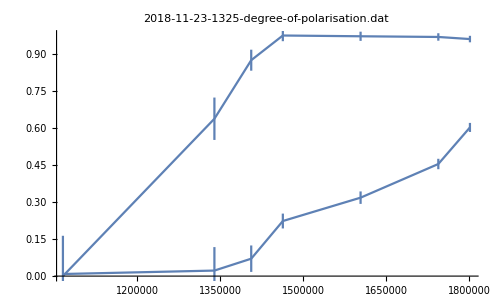

```mathematica
(* plotting specified files without correct x-axis values *)
listOfPlots={1};
pPlots=ErrorListPlot[p[[#]],Joined->True,PlotLabel->FileNameTake[files[[#]]],ImageSize->Medium]&/@listOfPlots;
tPlots=ErrorListPlot[t[[#]],Joined->True,PlotLabel->FileNameTake[files[[#]]],ImageSize->Medium]&/@listOfPlots;
Show[pPlots,tPlots]
```

```mathematica
t[[1]][[9]]
```

Part::partw: Part 9 of {{{1065340,0.00841819},ErrorBar[0.154765]},{{1339130,0.0223309},ErrorBar[0.0950229]},{{1405670,0.0704708},ErrorBar[0.0534905]},{{1462820,0.222906},ErrorBar[0.030076]},{{1603320,0.317472},ErrorBar[0.0252016]},{{1743820,0.453776},ErrorBar[0.0210795]},{{1800970,0.601774},ErrorBar[0.0183048]}} does not exist.

{{{1065340,0.00841819},ErrorBar[0.154765]},{{1339130,0.0223309},ErrorBar[0.0950229]},{{1405670,0.0704708},ErrorBar[0.0534905]},{{1462820,0.222906},ErrorBar[0.030076]},{{1603320,0.317472},ErrorBar[0.0252016]},{{1743820,0.453776},ErrorBar[0.0210795]},{{1800970,0.601774},ErrorBar[0.0183048]}}⟦9⟧

```mathematica
intensities[[1]][[9]]
pol[[1]][[9]]
```

{3815.5,3868.5,124.125,110.375}

0.963053